```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Spatial Mappings of an Image

There are three “kinds” of functions that are common in image processing: filters (linear, nonlinear, and morphological), spatial mappings, and transforms. Filters change the value of the pixels based on the values of all the pixels in a neighborhood. Spatial mappings leave the values of the pixels intact (more or less), but move them from one spatial location to another. Transforms calculate the values of the output pixels by looking at the complete image. This notebook discusses spatial mappings which can be as simple as a rotation or as complex as a texture mapping onto a 3D surface.

```mathematica
TableForm[{{Hyperlink["PointRec",{"visualVocabSpatialMaps.nb","labelPointRec"}],labelPointRec},{Hyperlink["RotateLL",{"visualVocabSpatialMaps.nb","labelRotateLL"}],labelRotateLL},{Hyperlink["Affine",{"visualVocabSpatialMaps.nb","labelAffine"}],labelAffine},{Hyperlink["Power",{"visualVocabSpatialMaps.nb","labelPower"}],labelPower},{Hyperlink["Torus",{"visualVocabSpatialMaps.nb","labelTorus"}],labelTorus},{Hyperlink["ExpCone",{"visualVocabSpatialMaps.nb","labelExpCone"}],labelExpCone},{Hyperlink["ImTrans",{"visualVocabSpatialMaps.nb","labelImTrans"}],labelImTrans},{Hyperlink["TransSpline",{"visualVocabSpatialMaps.nb","labelTransSpline"}],labelTransSpline}}]
```

PointRecvisualVocabSpatialMaps.nblabelPointRecvisualVocabSpatialMaps.nb | Rotation and scaling require interpolation
RotateLLvisualVocabSpatialMaps.nblabelRotateLLvisualVocabSpatialMaps.nb | Rotation about the lower left corner
AffinevisualVocabSpatialMaps.nblabelAffinevisualVocabSpatialMaps.nb | General linear mappings have 6-degrees of freedom can stretch, scale, flip, translate, and rotate
PowervisualVocabSpatialMaps.nblabelPowervisualVocabSpatialMaps.nb | This nonlinear map takes (x,y) to (x^s,y^t)
TorusvisualVocabSpatialMaps.nblabelTorusvisualVocabSpatialMaps.nb | Mapping images onto the surface of a torus
ExpConevisualVocabSpatialMaps.nblabelExpConevisualVocabSpatialMaps.nb | Mapping images onto the surface of an exponential cone
ImTransvisualVocabSpatialMaps.nblabelImTransvisualVocabSpatialMaps.nb | Nonlinear spatial mappings using ImageTransformation[ ]
TransSplinevisualVocabSpatialMaps.nblabelTransSplinevisualVocabSpatialMaps.nb | Click and drag at the intersections to warp the image

Important functions in this notebook include AffineTransform[ ] which conducts linear spatial mappings and ImageTransformation[] which conducts nonlinear spatial transformations. Most general of all are ParametricPlot[ ] and ParametricPlot3D[ ], which are ideal for arbitrary spatial mappings, though their syntax is more demanding.

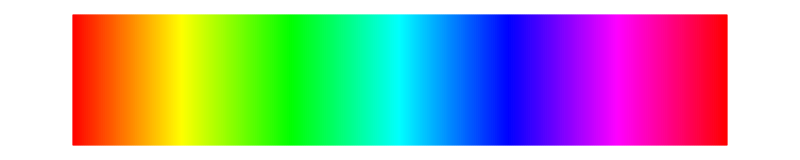

```mathematica
specLine
```

Underlying all spatial mappings is the need for interpolation, where the value at an unknown intermediate spatial position must be estimated based on known nearby values. To see why this occurs, consider rotation. If the image were printed on a piece of paper, there would be no problem since the paper can be easily rotated and the image would rotate with it. But in a digital representation, all the points must lie on a regular grid. Consider an image that takes on pixel values at each of the blue dots in the image below. The red points show the locations where the image ought to have points once it is rotated by a small amount; almost none of the red points coincide with blue points, and hence the values at the red locations must be inferred from the nearby blue values. The process of interpolation is explored in detail here.

```mathematica
labelPointRec="Rotation and scaling require interpolation";infoPointRec="The pixels of an image lie at the blue points. The pixels of the transformed image lie on the red points.\n\nThis example demonstrates two kinds of transformations with the sliders: rotation and scaling.\n\nSince most of the red and blue points are not at the same location, it is necessary to estimate what the value should be at the desired locations.\n\nThis estimation is called interpolation.";
pointRec=Point[Flatten[Table[{i,j},{i,1,12},{j,1,8}],1]];
Manipulate[Show[Graphics[{Blue,pointRec}],Graphics[{Red,Scale[Rotate[pointRec,θ],scale]}]],{{θ,0.01,"rotation"},-Pi/8,Pi/8},Row[{Control[{{scale,1,"scale"},0.9,1.1}],Spacer[20],info[infoPointRec]}],
FrameLabel->Style[labelPointRec,Medium],TrackedSymbols->{θ,scale},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

There are a large number of linear and nonlinear spatial mappings that can sensibly be applied to images. All such transformations have a general form that the value of the pixel at location {x,y} is mapped to {f[x,y], g[x,y]} where f[ ] and g[ ] are two functions. Common linear mappings include rotations, reflections, and shears. When the function includes an offset such as a translation, the map is called affine. More general (nonlinear) functions include arbitrary f[ ] and g[ ]. Some examples of named mappings and their internal representation are

```mathematica
{RotationTransform[θ],ReflectionTransform[{1,-1}],TranslationTransform[{x,y}],AffineTransform[{{{a11,a12},{a21,a22}},{b1,b2}}]}
```

{TransformationFunction[(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)],TransformationFunction[(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)],TransformationFunction[(1 | 0 | x
0 | 1 | y
0 | 0 | 1)],TransformationFunction[(a11 | a12 | b1
a21 | a22 | b2
0 | 0 | 1)]}

For the most part, it is not necessary to pay particular attention to the mathematical forms of representation of such functions, but if it becomes necessary, these forms are discussed here. When these functions are applied to images, they take each pixel value at location {x,y,1} and map them to the location TransformationMatrix.{x,y,1}. The simplest of the rotation functions rotates about the lower left hand corner of the image.

```mathematica
labelRotateLL="Rotation about the lower left corner";
infoRotateLL="Change the angle to rotate the image\n\nObserve the black edges that appear\n\nObserve the jagged edges are more noticeable when the color contrast is stark";
Manipulate[Show[ImageTransformation[allImagesColor[[i]],RotationTransform[θ]],ImageSize->{400}],{{θ,0,"angle θ"},-Pi/3,Pi/3},Row[{Control[{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoRotateLL]}],
FrameLabel->Style[labelRotateLL,Medium],TrackedSymbols->{θ,i},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦10⟧ is longer than depth of object.

Image`SpatialOperationsDump`ImageTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦10⟧.

Show::gtype: Image`SpatialOperationsDump`ImageTransformation is not a type of graphics.

Part::partd: Part specification allImagesColor⟦10⟧ is longer than depth of object.

Image`SpatialOperationsDump`ImageTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦10⟧.

Show::gtype: Image`SpatialOperationsDump`ImageTransformation is not a type of graphics.

HW: Make a demonstration of the Reflection or Translation function.

```mathematica
specLine
```

-Graphics-

A general affine transformation has six parameters, and can accomplish rotations, shears, translations, and reflections.

```mathematica
labelAffine="General linear mappings have 6-degrees of freedom can stretch, scale, flip, translate, and rotate";
infoAffine="Play with the coefficients:\n\nThe b parameters translate (shift) the image left/right and up/down\n\nParameters a21 and a12 shear the image\n\nParameters a11 and a22 scale the image\n\nMaking a11 and/or a22 negative flips the image";Manipulate[GraphicsRow[{AffineTransform[{{{a11,a12},{a21,a22}},{b1,b2}}],ImageTransformation[allImagesColor[[i]],AffineTransform[{{{a11,a12},{a21,a22}},{b1,b2}}]]},ImageSize->{600}],{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},
Row[{Control[{{a11,1},-1,1}],Spacer[20],Control[{{a12,0},-1,1}]}],Row[{Control[{{a21,1},-1,1}],Spacer[20],Control[{{a22,1},-1,1}]}],Row[{Control[{{b1,0},-1,1}],Spacer[20],Control[{{b2,0},-1,1}],Spacer[20],info[infoAffine]}],
FrameLabel->Style[labelAffine,Medium],TrackedSymbols->{i,a11,a12,a21,a22,b1,b2},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦10⟧ is longer than depth of object.

Image`SpatialOperationsDump`ImageTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦10⟧.

```mathematica
specLine
```

-Graphics-

More general methods can be used to define any function that represents the RGB values of an image at every possible point in space, even between the actual pixel value locations. Images can be mapped, distorted or warped in space by defining a transformation that maps into an interpolating function (such as the BSplineFunction used here). For example, this interactive example uses maps that raise to the s power in the x direction and raise to the t power in the y direction.

```mathematica
labelPower="This nonlinear map takes (x,y) to (x^s,y^t) using spline interpolation";
infoPower="The s and t parameters control the nonlinear warping of the x and y axes.\n\nExplain (in terms of the mapping on 0-1) why the squishing/stretches occurs";
Manipulate[img=allImagesColor[[i]];colorfun=BSplineFunction[ImageData[img],SplineDegree->1];
aspImg=ImageDimensions[img][[2]]/ImageDimensions[img][[1]];ParametricPlot[{u^s,v^t},{u,0,1},{v,0,1},ColorFunction->{colorfun[1-#4,#3]&},MaxRecursion->0,Mesh->None,PlotPoints->ControlActive[20,200],Frame->None,Axes->None,BoundaryStyle->None,AspectRatio->aspImg,ImageSize->{500}],
Row[{Control[{{i,vanHouse,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoPower]}],
{{s,1},0.1,5},
{{t,1},0.1,5},
FrameLabel->Style[labelPower,Medium],TrackedSymbols->{i,s,t},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦2⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦2⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

ImageDimensions::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Part::partw: Part 2 of ImageDimensions[allImagesColor⟦2⟧] does not exist.

ImageDimensions::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Part::partd: Part specification allImagesColor⟦2⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦2⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

ImageDimensions::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Part::partw: Part 2 of ImageDimensions[allImagesColor⟦2⟧] does not exist.

ImageDimensions::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Part::partd: Part specification allImagesColor⟦2⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦2⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

ImageDimensions::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Part::partw: Part 2 of ImageDimensions[allImagesColor⟦2⟧] does not exist.

ImageDimensions::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

The following is the same transformation applied using the ImageForwardTransformation function. The syntax is simpler, and the overall results are similar to the spline method above, except for details of how the edges are handled and how the interpolation is done.

```mathematica
labelPower="This map takes (x,y) to (x^s,y^t) using ImageForwardTransformation";
infoPower="The s and t parameters control the nonlinear warping of the x and y axes.\n\nExplain (in terms of the mapping on 0-1) why the squishing/stretches occurs";
warp[s_,t_]:={#[[1]]^s,#[[2]]^t}&;
Manipulate[img=allImagesColor[[i]];
Image[ImageForwardTransformation[img,warp[s,t]],ImageSize->{500}],
Row[{Control[{{i,vanHouse,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoPower]}],
{{s,1},0.1,5},
{{t,1},0.1,5},
FrameLabel->Style[labelPower,Medium],TrackedSymbols->{i,s,t},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦2⟧ is longer than depth of object.

ImageForwardTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Image::imgarray: The specified argument ImageForwardTransformation[allImagesColor⟦2⟧,warp[1.99,1.66]] should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification allImagesColor⟦2⟧ is longer than depth of object.

ImageForwardTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Image::imgarray: The specified argument ImageForwardTransformation[allImagesColor⟦2⟧,warp[1.99,1.66]] should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification allImagesColor⟦2⟧ is longer than depth of object.

ImageForwardTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦2⟧.

Image::imgarray: The specified argument ImageForwardTransformation[allImagesColor⟦2⟧,warp[1.99,1.66]] should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
specLine
```

-Graphics-

The same procedure works in mapping the image to a 3D surface using the parametric plot function ParameterPlot3D[ ]. The image is mapped here onto the surface of a torus, which can be moved interactively using the mouse.

```mathematica
labelTorus="Mapping images onto the surface of a torus";
infoTorus="Choose an image and use the mouse to rotate the torus\n\nWhat discontinuities can you see in the mapped image?\n\nThe variable u controls the radial circle (verify by plotting u from 0 to Pi)\n\nWhat is inside the donut?\n\nThe variable v controls the width of the donut (verify by plotting v from 0 to Pi)\n\nWhat is underneath the half torus?";
Manipulate[img=allImagesColor[[i]];colorfun=BSplineFunction[ImageData[img],SplineDegree->1];
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]}},{u,-Pi,Pi},{v,-Pi,Pi},ColorFunction->{colorfun[1-#5,#4]&},ViewPoint->{Pi/2,Pi,1},PlotPoints->200,MaxRecursion->0,Mesh->None,Axes->None,BoundaryStyle->None,ImageSize->{500}],Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoTorus]}],FrameLabel->Style[labelTorus,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦11⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦11⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦11⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partd: Part specification allImagesColor⟦11⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦11⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦11⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

```mathematica
specLine
```

-Graphics-

The image is mapped here onto the surface of an exponential cone. Again, the surface can be rotated at will using the mouse.

```mathematica
labelExpCone="Mapping images onto the surface of an exponential cone";
infoExpCone="Choose an image and use the mouse to rotate the exponential cone.\n\nWhat discontinuities can you see in the mapped image?\n\nWhat is the relationship between v and the length of the cone?\n\nWhat is inside the cone?\n\nChange the values over which u is plotted in order to look inside.";
Manipulate[img=allImagesColor[[i]];
colorfun=BSplineFunction[ImageData[img],SplineDegree->1];
ParametricPlot3D[{v Cos[u],v Sin[u],0.5/Abs[v Exp[I u]]},{u,-Pi,Pi},{v,0,1},ColorFunction->{colorfun[1-#5,#4]&},ViewPoint->{Pi/2,Pi,1},PlotPoints->200,MaxRecursion->0,Mesh->None,Axes->None,BoundaryStyle->None,ImageSize->{500}],Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoExpCone]}],FrameLabel->Style[labelExpCone,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦11⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦11⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦11⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

Part::partd: Part specification allImagesColor⟦11⟧ is longer than depth of object.

ImageData::imginv: Expecting an image or graphics instead of allImagesColor⟦11⟧.

BSplineFunction::invcpts: ImageData[allImagesColor⟦11⟧] should be a rectangular array of machine-sized real numbers of any depth, whose dimensions are greater than 1.

HW: Create a mapping that places one or more images on the six faces of a cube.

HW: Create a mapping that places an image on the surface of a sphere.

HW: Create a mapping that places an image on the surface of a Moebius strip.

```mathematica
(* Manipulate[ParametricPlot3D[{4 Cos[a]+r Cos[a] Cos[a/2],4 Sin[a]+r Sin[a] Cos[a/2],r Sin[a/2]},{a,0,4 π},{r,-(3/2),3/2},Boxed->False,Axes->False,Mesh->False,PlotPoints->{100,2},PlotStyle->{EdgeForm[],FaceForm[Directive[Texture[img]],None]},TextureCoordinateFunction->({#4-t,#5}&),PerformanceGoal->"Quality"],{t,0,1}] *)
```

```mathematica
specLine
```

-Graphics-

The Mathematica syntax using the ColorFunction can be a bit confusing. In many situations it is possible to use the somewhat simpler ImageTransformation[ ] function, which handles some of the above details more cleanly.

```mathematica
labelImTrans="Nonlinear spatial mappings using ImageTransformation[ ]";
infoImTrans="Observe the behavior of the mapping for a variety of values of s.\n\nAs s approaches 2π, explain what you see.\n\nExplain the image as s approaches zero.\n\nWhat sorts of symmetry appear when s=π?";
Manipulate[img=allImagesColor[[i]];
Show[ImageTransformation[img,Tan[s #]&,Padding->"Periodic"],ImageSize->{600}],
{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},
Row[{Control[{{s,1},0.01,2 Pi}],Spacer[20],info[infoImTrans]}],FrameLabel->Style[labelImTrans,Medium],TrackedSymbols->{i,s},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦9⟧ is longer than depth of object.

ImageTransformation::imginv: Expecting an image or graphics instead of allImagesColor⟦9⟧.

Show::gtype: ImageTransformation is not a type of graphics.

```mathematica
specLine
```

-Graphics-

Here is a way of combining many linear maps to warp an image. This demonstration is based on “Image Warping” from the Wolfram Demonstrations Project. Place the mouse on the image and drag the grid lines around. Choose the number of possible tie points using the grid size option, and the interpolation method using the radio buttons. The resolution is intentionally low at the start so that the calculations are quick. Increase the resolution for higher fidelity.

```mathematica
labelTransSpline="Click and drag at the intersections to warp the image";
infoTransSpline="Place the mouse on the image and drag the grid lines around. Choose the number of possible tie points using the grid size option, and the interpolation method using the radio buttons. The resolution is intentionally low at the start so that the calculations are quick. Increase the resolution for higher fidelity.\n\nAdjust the grid lines to make the Milkmaid's face as large as possible.\n\n Adjust the grid lines to make the Milkmaid's face as small as possible.";
Manipulate[
If[ii=!=previi,img=allImagesColor[[ii]];colfun=BSplineFunction[ImageData[img],SplineDegree->1];previi=ii;aspImg=ImageDimensions[img][[2]]/ImageDimensions[img][[1]];];
If[n=!=prevn,pts=Flatten[Table[{i,j},{i,0,1,1/(n-1)},{j,0,1,1/(n-1)}],1];
If[approx,sOrder=n-1,sOrder=2];prevn=n];
If[approx=!=prevapprox,If[approx,sOrder=n-1,sOrder=2];prevapprox=approx];
If[approx,f=BSplineFunction[Partition[pts,n],SplineDegree->sOrder,Method->{"Extrapolation"->"Clamp"}],
f=Interpolation[Flatten[Table[{{N[1/(n-1)]i,N[1/(n-1)]j},pts[[n i+j+1]]},{i,0,n-1},{j,0,n-1}],1],Method->"Spline",InterpolationOrder->sOrder]];
ParametricPlot[f[u,v],{u,0,1},{v,0,1},ColorFunction->(colfun[1-#4,#3]&),MaxRecursion->0,PlotPoints->ControlActive[20,plotPoints],Mesh->None,AspectRatio->aspImg,Frame->None,Axes->None,BoundaryStyle->None,Epilog->{Gray,Opacity[.7],Line[Partition[pts,n]],Line[Transpose[Partition[pts,n]]]},ImageSize->{600},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.03],FrameTicks->None],
"None"->{{pts,Flatten[Table[{i,j},{i,0,1,.25},{j,0,1,.25}],1]},{0,0},{1,1},Locator,Appearance->None},
Row[{Control[{{ii,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoTransSpline]}],
Row[{Control[{{n,4,"grid size"},4,8,2,ControlType->RadioButton}],Spacer[20],
Control[{{approx,True,"method"},{False->"B-spline",True->"Bézier surface"},ControlType->RadioButton}],Spacer[20],Control[{{plotPoints,100,"resolution"},{100,200,500}}]}],
{{previi,0},ControlType->None},
{{prevn,5},ControlType->None},
{{prevapprox,True},ControlType->None},
{colfun,ControlType->None},
{f,ControlType->None},
FrameLabel->Style[labelTransSpline,Medium],TrackedSymbols->{ii,n,approx,plotPoints,previi,prevn,prevapprox,colfun,f,pts},SaveDefinitions->saveDef]
```

BSplineFunction::invdeg: Value of option SplineDegree -> sOrder should be a positive integer, or a list of positive integers.

General::stop: Further output of BSplineFunction::invdeg will be suppressed during this calculation.

More details on how such geometric distortions are actually calculated can be found here.